3.20144+0.0307382 x-7.73495×10^-6 x^2+1.70945×10^-9 x^3-1.43806×10^-13 x^4

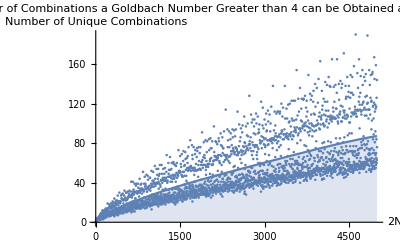

```mathematica
(*Loading the table from a csv generated by a C++ program*)
primes := Drop[Import["/home/jatin/Documents/Classes/Spring_2018/PHY110C/Final_proj/primes.csv"],1]
(*Col 1: A prime number p, Col 2: Another prime number q, Col 3: The sum of p and q which is an even number*)
freq := Tally[primes[[All, 3]]] (*Tally the number of times an even number shows up in the table, i.e. the number of combinations to get that number*)

line = Fit[freq, {1,x, x^2,x^3,x^4},x](*Quartic fit for the data*)
p1:=DiscretePlot[line, {x, 4, 5000, 2}](*Plotting the line*)

Show[ListPlot[freq, AxesLabel->{Style["2N", Bold,FontSize->14],Style["Number of Unique Combinations",Bold, FontSize->14]}, PlotLabel->Style["The Number of Combinations a Goldbach Number Greater than 4 can be Obtained as the sum of two Primes", FontSize->18]], p1]
```

-7.25306+0.570185 x-0.000035398 x^2+1.19406×10^-8 x^3-1.2964×10^-12 x^4

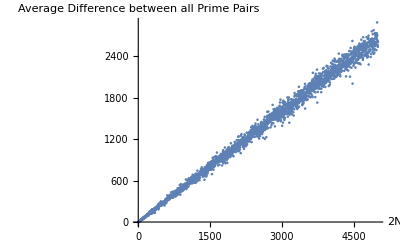

```mathematica
diff := Drop[Import["/home/jatin/Documents/Classes/Spring_2018/PHY110C/Final_proj/Difference.csv"], 1]
(*clearSystemCache[]
column := Table[{primes[[i]][[2]]- primes[[i]][[1]]}, {i, 1, Length[primes]}]
diff2 := Transpose[Insert[Transpose[primes],column]]
diff3 := GatherBy[diff2, #[[3]]&]
Show[ListPlot[Table[{x[[1,3]],N[Mean[x[[All,-1]]]]},{x,diff3}]]]*)
line3 = Fit[diff, {1,x, x^2,x^3,x^4},x]
Show[ListPlot[diff], AxesLabel->{Style["2N", Bold,FontSize->14],Style["Average Difference between all Prime Pairs",Bold, FontSize->14]}]
```

650.433-0.0652917 x-0.0000409228 x^2+1.14744×10^-8 x^3-1.17032×10^-12 x^4

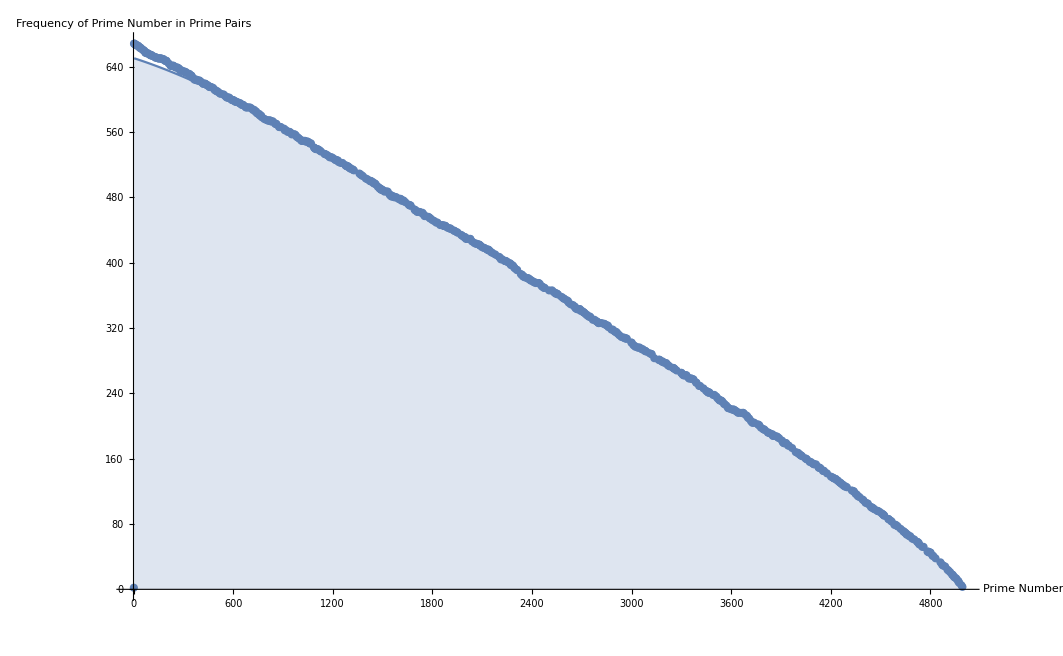

```mathematica
(*This graph shows the frequency of a prime numbers in the pairs used to obtain even numbers*)
joined := Join[primes[[All, 1]], primes[[All, 2]]]
j2 := Tally[joined]

line2 = Fit[j2, {1,x, x^2,x^3,x^4},x](*Quartic fit for the data*)
p2:=DiscretePlot[line2, {x, 4, 5000, 2}](*Plotting the line*)

Show[ListPlot[j2, AxesLabel->{Style["Prime Number", Bold,FontSize->14],Style["Frequency of Prime Number in Prime Pairs",Bold, FontSize->14]}],p2]
```